# Project Euler

#### 1 Multiples of 3 and 5

If we list all the natural numbers between 10 that are multiples of 3 or 5, we get 3, 5, 6 and 9. The sum of these multiples is 23. 
Find the sum of all the multiples of 3 or 5 below 1000.

```mathematica
Total[Select[Range[999],Or@@Thread[Divisible[#,{3,5}]]&]]
```

233168

#### 2 Even Fibonacci numbers

Each new term in the Fibonacci sequence is generated by adding the previous two terms. By starting with 1 and 2, the first 10 terms will be:
 		1, 2, 3, 5, 8, 13, 21, 34, 55, 89, ...
By considering the terms in the Fibonacci sequence whose values do not exceed four million, find the sum of the even-valued terms.

```mathematica
Block[{$IterationLimit = Infinity},
    Function[With[{a=#1,b=#2,s=#3},
        If[a≥4000000,s,#0[b,a+b,If[EvenQ[a],s+a,s]]]]][1,2,0]]
```

4613732

#### 3 Largest prime factor

The prime factors of 13195 are 5, 7, 13 and 29.
What is the largest prime factor of the number 600851475143?

```mathematica
Max[First/@FactorInteger[600851475143]]
```

6857

#### 4 Largest palindrome product

A palindromic number reads the same both ways. The largest palindrome made from the product of two 2-digit numbers is 9009 = 91 × 99.
Find the largest palindrome made from the product of two 3-digit numbers.

```mathematica
Times@@SelectFirst[PalindromeQ[Times@@#]&]@
    SortBy[-Times@@#&]@
        Subsets[Range[100,999],{2}]
```

906609

#### 5 Smallest multiple

2520 is the smallest number that can be divided by each of the numbers from 1 to 10 without any remainders.
What is the smallest positive number that is evenly divisible by all of the numbers from 1 to 20?

```mathematica
LCM@@Range[20]
```

232792560

#### 6 Sum square difference

The sum of the squares of the first ten natural numbers is,
            1^2+2^2+...+10^2=385
The square of the sum of the first ten natural numbers is,
            (1+2+...+10)^2=55^2=3025
Hence the difference between the sum of the squares of the first ten natural numbers and the square of the sum is 3025 - 385 = 2640.
Find the difference between the sum of the squares of the first one hundred natural numbers and the square of the sum.

```mathematica
Total[Range[100]]^2 - Total[Range[100]^2]
```

25164150

#### 7 10001st prime

By listing the first six prime numbers: 2, 3, 5, 7, 11, and 13, we can see that the 6th prime is 13.
What is the 10 001st prime number?

```mathematica
Prime[10001]
```

104743

#### 8 Largest product in series

The four adjacent digits in the 1000-digit number that have the greatest product are 9×9×8×9=5932.
Find the thirteen adjacent digits in the 1000-digit number that have the greatest product. What is the value of this product.

```mathematica
p08input=7316717653133062491922511967442657474235534919493496983520312774506326239578318016984801869478851843858615607891129494954595017379583319528532088055111254069874715852386305071569329096329522744304355766896648950445244523161731856403098711121722383113622298934233803081353362766142828064444866452387493035890729629049156044077239071381051585930796086670172427121883998797908792274921901699720888093776657273330010533678812202354218097512545405947522435258490771167055601360483958644670632441572215539753697817977846174064955149290862569321978468622482839722413756570560574902614079729686524145351004748216637048440319989000889524345065854122758866688116427171479924442928230863465674813919123162824586178664583591245665294765456828489128831426076900422421902267105562632111110937054421750694165896040807198403850962455444362981230987879927244284909188845801561660979191338754992005240636899125607176060588611646710940507754100225698315520005593572972571636269561882670428252483600823257530420752963450;

Max@Map[Apply[Times]]@Partition[IntegerDigits[p08input],13,1]
```

23514624000

#### 9 Special Pythagorean triplet

A Pythagorean triplet is a set of three natural numbers, a<b<c, for which,
          a^2+b^2+c^2
For example, 3^2+4^2=9+16=25=5^2.
There exists exactly one Pythagorean triplet for which a+b+c=1000.
Find the product abc.

```mathematica
Catenate@Table[
With[{c=1000-a-b},If[c>0&&a^2+b^2==c^2, a b c, Nothing]], 
{a,1,1000}, {b,a,1000}]
```

{31875000}

#### 10 Summation of primes

The sum of the primes below 10 is 2+3+5+7=17.
Find the sum of all the primes below two million.

```mathematica
Sum[Prime[i],{i,PrimePi[2000000]}]
```

142913828922

#### 11 Largest product in a grid

In the 20×20 grid below, What is the greatest product of four adjacent numbers in the same direction (up, down, left, right, or diagonally) in the 20×20 grid?

```mathematica
p11matrix=({{8, 2, 22, 97, 38, 15, 0, 40, 0, 75, 4, 5, 7, 78, 52, 12, 50, 77, 91, 8}, {49, 49, 99, 40, 17, 81, 18, 57, 60, 87, 17, 40, 98, 43, 69, 48, 4, 56, 62, 0}, {81, 49, 31, 73, 55, 79, 14, 29, 93, 71, 40, 67, 53, 88, 30, 3, 49, 13, 36, 65}, {52, 70, 95, 23, 4, 60, 11, 42, 69, 24, 68, 56, 1, 32, 56, 71, 37, 2, 36, 91}, {22, 31, 16, 71, 51, 67, 63, 89, 41, 92, 36, 54, 22, 40, 40, 28, 66, 33, 13, 80}, {24, 47, 32, 60, 99, 3, 45, 2, 44, 75, 33, 53, 78, 36, 84, 20, 35, 17, 12, 50}, {32, 98, 81, 28, 64, 23, 67, 10, 26, 38, 40, 67, 59, 54, 70, 66, 18, 38, 64, 70}, {67, 26, 20, 68, 2, 62, 12, 20, 95, 63, 94, 39, 63, 8, 40, 91, 66, 49, 94, 21}, {24, 55, 58, 5, 66, 73, 99, 26, 97, 17, 78, 78, 96, 83, 14, 88, 34, 89, 63, 72}, {21, 36, 23, 9, 75, 0, 76, 44, 20, 45, 35, 14, 0, 61, 33, 97, 34, 31, 33, 95}, {78, 17, 53, 28, 22, 75, 31, 67, 15, 94, 3, 80, 4, 62, 16, 14, 9, 53, 56, 92}, {16, 39, 5, 42, 96, 35, 31, 47, 55, 58, 88, 24, 0, 17, 54, 24, 36, 29, 85, 57}, {86, 56, 0, 48, 35, 71, 89, 7, 5, 44, 44, 37, 44, 60, 21, 58, 51, 54, 17, 58}, {19, 80, 81, 68, 5, 94, 47, 69, 28, 73, 92, 13, 86, 52, 17, 77, 4, 89, 55, 40}, {4, 52, 8, 83, 97, 35, 99, 16, 7, 97, 57, 32, 16, 26, 26, 79, 33, 27, 98, 66}, {88, 36, 68, 87, 57, 62, 20, 72, 3, 46, 33, 67, 46, 55, 12, 32, 63, 93, 53, 69}, {4, 42, 16, 73, 38, 25, 39, 11, 24, 94, 72, 18, 8, 46, 29, 32, 40, 62, 76, 36}, {20, 69, 36, 41, 72, 30, 23, 88, 34, 62, 99, 69, 82, 67, 59, 85, 74, 4, 36, 16}, {20, 73, 35, 29, 78, 31, 90, 1, 74, 31, 49, 71, 48, 86, 81, 16, 23, 57, 5, 54}, {1, 70, 54, 71, 83, 51, 54, 69, 16, 92, 33, 48, 61, 43, 52, 1, 89, 19, 67, 48}});
submatrixMax[m_]:=
    Max[Times @@@ {
        m⟦1⟧,
        m⟦All,1⟧,
        Diagonal[m],
        {m⟦1,4⟧,m⟦2,3⟧,m⟦3,2⟧,m⟦4,1⟧}
    }];

Max@Flatten@Table[
    submatrixMax[p11matrix⟦row;;row+3,col;;col+3⟧],
    {row,1,17},{col,1,17}
]
```

70600674

#### 12 Highly divisible triangular number

The sequence of triangle numbers is generated by adding the natural numbers, So the 7^th triangle number would be 1+2+3+4+5+6+7=28. The first ten terms would be:
		1,3,6,10,15,21,28,36,45,55,...
Let us list the factors of the first seven triangle numbers:
		    1: 1
  3: 1,2,3,6
10: 1,2,5,10
15: 1,3,5,15
21: 1,3,7,21
28: 1,2,4,7,14,28
We can see that 28 is the first triangle number to have over five divisors.
What is the value of the first triangle number to have over five hundred divisors?

```mathematica
Block[{$IterationLimit=Infinity},
  Function[If[#2≠0&&Length@Divisors[#2]>500,#2,#0[#1+1,#2+#1]]][1,0]]
```

76576500

#### 13 Large sum

Work out the first ten digits of the sum of the following one-hundred 50-digit numbers.

```mathematica
p13input=Flatten@Import[FileNameJoin[{NotebookDirectory[],"p13_data.txt"}],"Table"];
FromDigits@Take[IntegerDigits@Total@p13input,10]
```

5537376230

#### 14 Longest Collatz sequence

The following iterative sequence is defined for the set of positive integers:
		n → n/2 (n is even)
n → 3n+1 (n is odd)
Using the rule above and starting with 13, we generate the following sequence:
		13→40→20→10→5→16→8→4→2→1
It can be seen that this sequence (starting at 13 and finishing at 1) contains 10 terms. Although it has not been proved yet (Collatz Problem), it is thought that all starting numbers finish at 1.
Which starting number, under one million, produces the longest chain?
NOTE: Once the chain starts the terms are allowed to go above one million.

```mathematica
Module[{collatz,chain},
    collatz[n_?EvenQ]:=n/2;
    collatz[n_?OddQ]:=3n+1;
    chain[1]=1;
    chain[n_]:=chain[n]=chain[collatz[n]]+1;
    MaximalBy[Range[1000000],chain]
]//AbsoluteTiming
```

{12.7396,{837799}}

#### 15 Lattice paths

Starting in the top left corner of a 2×2 grid, and only being able to move to the right and down, there are exactly 6 routes to the bottom right corner.

				-Graphics-
How many such routes are there through a 20×20 grid?

```mathematica
Module[{routes},
    routes[0,_]=routes[_,0]=1;
    routes[m_,n_]:=routes[m,n]=routes[m,n-1]+routes[m-1,n];
    routes[20,20]
]
```

137846528820

```mathematica
Binomial[40,20]
```

137846528820

#### 16 Power digit sum

2^15=32768 and the sum of its digits is 3+2+7+6+8=26.
What is the sum of the digits of the number 2^1000?

```mathematica
Total@IntegerDigits[2^1000]
```

1366

#### 17 Number letter counts

If the number 1 to 5 are written out in words: one, two, three, four, five, then there are 3 + 3 + 5 + 4 + 4 = 19 letters used in total.
If all the numbers from 1 to 1000 (one thousand) inclusive were written out in words, how many letters would be used?

NOTE: Do not count spaces or hyphens. For example, 342 (three hundred and forty-two) contains 23 letters and 115 (one hundred and fifteen) contains 20 letters. The use of “and” when writing out numbers is in compliance with British usage.

```mathematica
ClearAll[numerals];

numerals[0] = "zero";
numerals[1] = "one";
numerals[2] = "two";
numerals[3] = "three";
numerals[4] = "four";
numerals[5] = "five";
numerals[6] = "six";
numerals[7] = "seven";
numerals[8] = "eight";
numerals[9] = "nine";
numerals[10] = "ten";
numerals[11] = "eleven";
numerals[12] = "twelve";
numerals[13] = "thirteen";
numerals[14] = "fourteen";
numerals[15] = "fifteen";
numerals[16] = "sixteen";
numerals[17] = "seventeen";
numerals[18] = "eighteen";
numerals[19] = "nineteen";
numerals[20] = "twenty";
numerals[30] = "thirty";
numerals[40] = "forty";
numerals[50] = "fifty";
numerals[60] = "sixty";
numerals[70] = "seventy";
numerals[80] = "eighty";
numerals[90] = "ninety";

numerals::badarg = "The argument `1` is out of range.";
numerals[n_Integer] /; n<0||n≥10^9 := 
    (Message[numerals::badarg, n]; $Failed)
numerals[n_Integer] /; n<100 := 
    numerals[Floor[n/10]*10]<>"-"<>numerals[Mod[n,10]];
numerals[n_Integer] /; n<1000&&Divisible[n,100] := 
    numerals[n/100]<>" hundred";
numerals[n_Integer] /; n<1000 := 
    numerals[Floor[n/100]]<>" hundred and "<>numerals[Mod[n,100]];
numerals[n_Integer] /; n<10^6&&Divisible[n,10^3] := 
    numerals[n/10^3]<>" thousand";
numerals[n_Integer] /; n<10^6 := 
    numerals[Floor[n/10^3]]<>" thousand, "<>numerals[Mod[n,10^3]];
numerals[n_Integer] /; n<10^9 && Divisible[n,10^6] := 
    numerals[n/10^6]<>" million";
numerals[n_Integer] /; n<10^9 := 
    numerals[Floor[n/10^6]]<>" million, "<>numerals[Mod[n,10^6]];

Sum[StringLength@StringDelete[" "|"-"|","]@numerals[n],{n,1000}]
```

21124

#### 18 Maximum path sum I

By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.
							3
7 | 4
2 | 4 | 6
8 | 5 | 9 | 3
That is, 3+7+4+9=23.
Find the maximum total from top to bottom of  the triangle below:
NOTE: As there are only 16384 routes, it is possible to solve this problem by trying every route, However, Problem 67, is the same challenge with a triangle containing one-hundred rows; it cannot be solved by brute force, and requires a clever method! ;o)

```mathematica
p18input={{{{75}}}, {{{95, 64}}}, {{{17, 47, 82}}}, {{{18, 35, 87, 10}}}, {{{20, 04, 82, 47, 65}}}, {{{19, 01, 23, 75, 03, 34}}}, {{{88, 02, 77, 73, 07, 63, 67}}}, {{{99, 65, 04, 28, 06, 16, 70, 92}}}, {{{41, 41, 26, 56, 83, 40, 80, 70, 33}}}, {{{41, 48, 72, 33, 47, 32, 37, 16, 94, 29}}}, {{{53, 71, 44, 65, 25, 43, 91, 52, 97, 51, 14}}}, {{{70, 11, 33, 28, 77, 73, 17, 78, 39, 68, 17, 57}}}, {{{91, 71, 52, 38, 17, 14, 91, 43, 58, 50, 27, 29, 48}}}, {{{63, 66, 04, 68, 89, 53, 67, 30, 73, 16, 69, 87, 40, 31}}}, {{{04, 62, 98, 27, 23, 09, 70, 98, 73, 93, 38, 53, 60, 04, 23}}}};
Module[{sum,route,format,output},
    (* Just sum up the numbers *)
    sum[m_,row_,col_]:=
        If[row==Length[m],
            m⟦row,col⟧,
            m⟦row,col⟧+Max[sum[m,row+1,col],sum[m,row+1,col+1]]];

    (* Find route for the maximum total *)
    route[m_,row_,col_]:=
        If[row==Length[m],
            {m⟦row,col⟧,{{row,col}}},
            With[{left=route[m,row+1,col],right=route[m,row+1,col+1]},
                If[left⟦1⟧ > right⟦1⟧,
                    {m⟦row,col⟧ + left⟦1⟧,Prepend[left⟦2⟧, {row,col}]},
                    {m⟦row,col⟧ + right⟦1⟧,Prepend[right⟦2⟧, {row,col}]}]]];

    (* Visualize the route *)
    format[m_,route_]:=
         MapIndexed[
             Text[Style[IntegerString[#1,10,2],
                                      If[MemberQ[route,#2],Red,Black]]]&,
             m,{2}];
     output[m_,route_] :=
         Column[Map[Grid[{#}]&,format[m, route]],Center];

    With[{m=Flatten[p18input,2]},
        Column[{output[m, #2],"",#1}]&@@route[m,1,1]]
]
```

75
95 | 64
17 | 47 | 82
18 | 35 | 87 | 10
20 | 04 | 82 | 47 | 65
19 | 01 | 23 | 75 | 03 | 34
88 | 02 | 77 | 73 | 07 | 63 | 67
99 | 65 | 04 | 28 | 06 | 16 | 70 | 92
41 | 41 | 26 | 56 | 83 | 40 | 80 | 70 | 33
41 | 48 | 72 | 33 | 47 | 32 | 37 | 16 | 94 | 29
53 | 71 | 44 | 65 | 25 | 43 | 91 | 52 | 97 | 51 | 14
70 | 11 | 33 | 28 | 77 | 73 | 17 | 78 | 39 | 68 | 17 | 57
91 | 71 | 52 | 38 | 17 | 14 | 91 | 43 | 58 | 50 | 27 | 29 | 48
63 | 66 | 04 | 68 | 89 | 53 | 67 | 30 | 73 | 16 | 69 | 87 | 40 | 31
04 | 62 | 98 | 27 | 23 | 09 | 70 | 98 | 73 | 93 | 38 | 53 | 60 | 04 | 23

1074

#### 19 Counting Sundays

You are given the following information, but you may prefer to do some research for yourself.
	1 Jan 1900 was a Monday
	Thirty days has September, 
	April, June and November.
	All the rest have thirty-one, 
	Saving February alone,
	Which has twenty-eight, rain or shine.
	And on leap years, twenty-nine.
	A leap year occurs on any year evenly divisible by 4, but not on a century unless it is divisible by 400.
How many Sundays fell on the first of the month during the twentieth century (1 Jan 1901 to 31 Dec 2000)?

```mathematica
Sum[Boole[DateValue[DateObject[{y,m,1}],"DayName"]==Sunday],
  {y,1901,2000},{m,1,12}]
```

171

#### 20 Factorial digit sum

n! means n×(n-1)×...×3×2×1
For example, 10! = 10×9×...×3×2×1 = 3628800,
and the sum of the digits in the number 10! is 3+6+2+8+8+0+0=27.
Find the sum of the digits in the number 100!

```mathematica
Total@IntegerDigits[100!]
```

648

#### 21 Amicable numbers

Let d(n) be defined as the sum of proper divisors of n (numbers less than n which divide evenly into n).
If d(a)=b and d(b)=a, where a≠b, then a and b are an amicable pair and each of a and b are called amicable numbers.
For example, the proper divisors of 220 are 1, 2, 4, 5, 10, 11, 20, 22, 44, 55, and 100; therefore d(220)=284. The proper divisors of 284 are 1, 2, 4, 71 and 142; so d(284)=220.
Evaluate the sum of all the amicable numbers under 10000.

```mathematica
Module[{d,amicable},
    d[n_]:=Total@Divisors[n]-n;
    amicable[a_]:=d[a]≠a&&d[d[a]]==a;
    Sum[If[amicable[n],n,0],{n,10000}]
]
```

31626

#### 22 Name scores

Using names.txt, a 64K text file containing over five-thousand first names, begin by sorting it into alphabetical order. Then working out the alphabetical value for each name, multiply this value by its alphabetical position in the list to obtain a name score.
For example, when the list is sorted into alphabetical order, COLIN, which is worth 3 + 15 + 12 + 9 + 14 = 53, is the 938th name in the list. So, COLIN would obtain a score 938 × 53 = 49713.
What is the total of all the name scores in the file?

```mathematica
With[{names=First@Import["https://projecteuler.net/project/resources/p022_names.txt","CSV"]},
    Total@MapIndexed[Total[ToCharacterCode[#1]-64]*#2&,Sort[names]]]
```

{871198282}

#### 23 Non-abundant sums

A perfect number is a number for which the sum of its proper divisors is exactly equal to the number. For example, the sum of the proper divisors of 28 would be 1 + 2 + 4 + 7 + 14 = 28, which means that 28 is a perfect number.
A number n is called deficient if the sum of its proper divisors is less than n and it is called abundant if this sum exceeds n.
As 12 is the smallest abundant number, 1 + 2 + 3 + 4 + 6 = 16, the smallest number that can be written as the sum of two abundant numbers is 24. By mathematical analysis, it can be shown that all integers greater than 28123 can be written as the sum of two abundant numbers. However, this upper limit cannot be reduced any further by analysis even though it is known that the greatest number that cannot be expressed as the sum of two abundant numbers is less than this limit.
Find the sum of all the positive integers which cannot be written as the sum of two abundant numbers.

```mathematica
Module[{limits=Range[28123],abundant,absums},
    abundant[n_]:=abundant[n]=Total@Divisors[n]>2n;
    absums[n_]:=AnyTrue[Range[n/2],abundant[#]&&abundant[n-#]&];
    Fold[If[absums[#2],#1,#1+#2]&,0,limits]
] // AbsoluteTiming
```

{24.8206,4179871}

#### 24 Lexicographic permutations

A permutation is an ordered arrangement of objects. For example, 3124 is one possible permutation of the digits 1, 2, 3 and 4. If all of the permutations are listed numerically or alphabetically, we call it lexicographic order. The lexicographic permutations of 0, 1 and 2 are:
		012    021    102    120    201    210
What is the millionth lexicographic permutation of the digits 0, 1, 2, 3, 4, 5, 6, 7, 8 and 9?

```mathematica
FromDigits@Permutations[Range[0,9]]⟦1000000⟧
```

2783915460

#### 25 1000-digit Fibonacci number

The Fibonacci sequence is defined by the recurrence relation:
		F_n=F_(n-1)+F_(n-2), where F_1=1 and F_2=1.
Hence the first 12 terms will be:
		F_1=1
F_2=1
F_3=2
F_4=3
F_5=5
F_6=8
F_7=13
F_8=21
F_9=34
F_10=55
F_11=89
F_12=144
The 12th term, F_12, is the first term to contain three digits.
What is the index of the first term in the FIbonacci sequence to contain 1000 digits?

```mathematica
Block[{$IterationLimit=Infinity},
    Function[If[#1≥10^999,#3,#0[#2,#1+#2,#3+1]]][1,1,1]]
```

4782

#### 26 Reciprocal cycles

A unit fraction contains 1 in the numerator. The decimal representation of the unit fractions with denominators 2 to 10 are given:
		1/2 = 0.5
1/3 = 0.(3)
1/4 = 0.25
1/5 = 0.2
1/6 = 0.1(6)
1/7 = 0.(142857)
1/8 = 0.125
1/9 = 0.(1)
1/10 = 0.1
Where 0.1(6) means 0.1666666..., and has a 1-digit recurring cycle. It can be seen 1/7 has a 6-digit recurring cycle.
Find the value of d < 1000 for which 1/d contains the longest recurring cycle in its decimal fraction part.

```mathematica
MaximalBy[Range[1000],Length@RealDigits[1/#][[1,-1]]&]
```

{983}

#### 27 Quadratic primes

Euler discovered the remarkable quadratic formula:
		n^2+n+41
It turns out that the formula will produce 40 primes for the consecutive integers values 0≤n≤39. However, when n=40, 40^2+40+41=40(40+1)+41 is divisible by 41, and certainly when n=41, 41^2+41+41 is clearly divisible by 41.
The incredible formula n^2-79n+1601 was discovered, which produces 80 primes for the consecutive values 0≤n≤79. The product of the coefficients, -79 and 1601, is -126479.
Considering quadratics of the form:
		n^2+a n+b, where |a|<1000 and |b|≤1000
		where |n|is the modulus/absolute value of n
		e.g. |11|=11 and |-4|=4
Find the product of the coefficients, a and b, for the quadratic expression that produces the maximum number of primes for consecutive values of n, starting with n=0.

```mathematica
Module[{consecutive},
    consecutive[{a_,b_}]:=NestWhile[#+1&,0,PrimeQ[#^2+a#+b]&];
    Times@@Flatten@MaximalBy[consecutive]@Tuples[Range[-1000,1000],{2}]
]//AbsoluteTiming
```

{15.2046,-59231}

#### 28 Number spiral diagonals

Starting with the number 1 and moving to the right in a clockwise direction a 5 by 5 spiral is formed as follows:
				21 | 22 | 23 | 24 | 25
20 | 7 | 8 | 9 | 10
19 | 6 | 1 | 2 | 11
18 | 5 | 4 | 3 | 12
17 | 16 | 15 | 14 | 13
It can be verified that the sum of the numbers on the diagonals is 101.
What is the sum of the numbers on the diagonals in a 1001 by 1001 spiral formed in the same way?

```mathematica
1+Sum[4k^2-6k+6,{k,3,1001,2}]
```

669171001

Explain: For an n×n grid, and n being odd, the number in the four corners are given by: n^2,n^2-n+1,n^2-2n+2,n^2-3n+3. Adding these together gives the quadratic, 4 n^2-6n+6. Adding all the quadratics from 3 to n in steps of 2 to get the running total (don’t forget the 1 in the center.)

#### 29 Distinct powers

Consider all integer combinations of a^b for 2≤a≤5 and 2≤b≤5:
		2^2=4, 2^3=8, 2^4=16, 2^5=32
3^2=9, 3^3=27, 3^4=81, 3^5=243
4^2=16, 4^3=64, 4^4=256, 4^5=1024
5^2=25, 5^3=125, 5^4=625, 5^5=3125
If they are then placed in numerical order, with any repeats removed, we get the following sequence of 15 distinct terms:
		4, 8, 9, 16, 25, 27, 32, 64, 81, 125, 243, 256, 625, 1024, 3125
How many distinct terms are in the sequence generated by a^b for 2≤a≤100 and 2≤b≤100?

```mathematica
Length@DeleteDuplicates@Flatten@Array[Power,{99,99},{2,2}]
```

9183

#### 30 Digit fifth powers

Surprisingly there are only three numbers that can be written as the sum of fourth powers of their digits:
		1634 = 1^4+6^4+3^4+4^4
8208 = 8^4+2^4+0^4+8^4
9474 = 9^4+4^4+7^4+4^4
As 1=1^4 is not a sum it is not included.
The sum of these numbers is 1634 + 8208 + 9474 = 19316.
Find the sum of all the numbers that can be written as the sum of fifth powers of their digits.

Hint: It’s easy to proof that the maximum number should not exceeds 6 digits.

```mathematica
Sum[If[Total[IntegerDigits[n]^5]==n,n,0],{n,2,6*9^5}]
```

443839

#### 31 Coin sums

In England the currency is made up of pound, £, and pence, p, and there are eight coins in general circulation:
		1p, 2p, 5p, 10p, 20p, 50p, £1 (100p) and £2 (200p).
It is possible to make £2 in the following way:
		1×£1 + 1×50p +2×20p + 1×5p + 1×2p + 3×1p
How many different ways can £2 be made using any number of coins?

```mathematica
Module[{coinSums,cc,denomination},
    coinSums[amount_]:=cc[amount,8];
    cc[0,_]=1;
    cc[_,0]=0;
    cc[amount_,_]/;amount<0:=0;
    cc[amount_,coinKinds_]:=
        cc[amount,coinKinds-1]+cc[amount-denomination[coinKinds],coinKinds];
    denomination[1]=1;
    denomination[2]=2;
    denomination[3]=5;
    denomination[4]=10;
    denomination[5]=20;
    denomination[6]=50;
    denomination[7]=100;
    denomination[8]=200;
    coinSums[200]
]//AbsoluteTiming
```

{7.95911,73682}

#### 32 Pandigital products

We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once; for example, the 5-digit number, 15234, is 1 through 5 pandigital.
The product 7254 is unusual, as the identity, 39 × 186 = 7254, containing multiplicand, multiplier, and product is 1 through 9 pandigital.
Find the sum of all products whose multiplicand/multiplier/product identity can be written as a 1 through 9 pandigital.
HINT: Some products can be obtained in more than one way so be sure to only include it once in your sum.

```mathematica
Module[{pandigitalQ,pandigitalProductQ},
    pandigitalQ[n_][d_]:=
        FromDigits@Sort@Flatten@Thread@IntegerDigits[{d,n/d,n}]==123456789;
    pandigitalProductQ[n_]:=
        AnyTrue[pandigitalQ[n]]@DeleteCases[1|n]@Divisors[n];
    Total@Select[pandigitalProductQ]@Map[FromDigits]@Permutations[Range[9],{4}]
]//AbsoluteTiming
```

{1.29308,45228}

#### 33 Digit cancelling fractions

The fraction 49/98 is a curious fraction, as an inexperienced mathematician in attempting to simplify it may incorrectly believe that 49/98 = 4/8, which is correct, is obtained by cancelling the 9s.
We shall consider fractions like, 30/50 = 3/5, to be trivial examples.
There are exactly four non-trivial examples of this type of fraction, less than one in value, and containing two digits in the numerator and denominator.
If the product of these four fractions is given in its lowest common terms, find the value of the denominator.

```mathematica
cancellable[{n_,d_}]:=
    If[n/d≥1||Or@@Thread[Divisible[{n,d},10]]||Or@@Thread[Divisible[{n,d},11]],
        False,
        With[{
            nn=IntegerDigits[n]~Complement~IntegerDigits[d],
            dd=IntegerDigits[d]~Complement~IntegerDigits[n]
        },Length[nn]==Length[dd]==1&&n/d==First[nn/dd]]];
Denominator[Times@@(Divide@@@Select[cancellable]@Subsets[Range[10,99],{2}])]
```

1

#### 34 Digit factorials

145 is a curious number, as 1!+4!+5! = 1+24+120=145.
Find the sum of all numbers which are equal to the sum of the factorial of their digits.
Note: as 1! = 1 and 2! = 2 are not sums they are not included.
Hint: The upper bound in theory should be 7×9!, but in practical 50000 is enough.

```mathematica
Sum[If[Total@Factorial@IntegerDigits[i]==i,i,0],{i,3,50000}]
```

40730

#### 35 Circular primes

The number, 197, is called a circular prime because all rotations of the digits: 197, 971, and 719, are themselves prime.
There are thirteen such primes below 100: 2, 3, 5, 7, 11, 13, 17, 31, 37, 71, 73, 79, and 97.
How many circular primes are there below one million?

```mathematica
circularPrimeQ[p_]:=
    With[{digits=IntegerDigits[p]},
        AllTrue[PrimeQ@*FromDigits]@NestList[RotateLeft,digits,Length[digits]-1]];
Sum[Boole@circularPrimeQ@Prime[i],{i,PrimePi[10^6]}]
```

55

#### 36 Double-base palindromes

The decimal number, 585=1001001001_2 (binary), is palindromic in both bases.
Find the sum of all numbers, less than one million,which are palindromic in base 10 and base 2.
(Please note that the palindromic number, in either case, may not include leading zeros.)

```mathematica
Sum[If[PalindromeQ[n]&&n==IntegerReverse[n,2],n,0],{n,10^6}]//AbsoluteTiming
```

{6.35381,872187}

#### 37 Truncatable primes

The number 3797 has an interesting property. Being prime itself, it is possible to continuously remove digits from left to right, and remain prime at each stage: 3797, 797, 97, and 7. Similarly we can work from right to left: 3797, 379, 37, and 3.
Find the sum of the only eleven primes that are both truncatable from left to right and right to left.
NOTE: 2, 3, 5, and 7 are not considered to be truncatable primes.

```mathematica
Module[{truncatablePrimeQ,findTruncatablePrimes},
    truncatablePrimeQ[p_]:=
        With[{digits=IntegerDigits[p]},
            AllTrue[PrimeQ@*FromDigits]@NestList[Drop[#,1]&,digits,Length[digits]-1]&&
            AllTrue[PrimeQ@*FromDigits]@NestList[Drop[#,-1]&,digits,Length[digits]-1]
        ];

    findTruncatablePrimes[p_,n_,s_]:=
        Which[
            n≥11,
                s,
            truncatablePrimeQ[p],
                findTruncatablePrimes[NextPrime[p],n+1,s+p],
            True,
                 findTruncatablePrimes[NextPrime[p],n,s]
        ];

    Block[{$IterationLimit=Infinity},findTruncatablePrimes[11,0,0]]
]
```

748317

#### 38 Pandigital multiples

Take the number 192 and multiply it by each of 1, 2, and 3:
		192 × 1 = 192
		192 × 2 = 384
		192 × 3 = 576
By concatenating each product we get the 1 to 9 pandigital, 192384576. We will call 192384576 the concatenated product of 192 and (1,2,3).
The same can be achieved by starting with 9 and multiplying by 1, 2, 3, 4, and 5, giving the pandigital, 918273645, which is the concatenated product of 9 and (1,2,3,4,5).
What is the largest 1 to 9 pandigital 9-digit number that can be formed as the concatenated product of an integer with (1,2,...,n) where n > 1?
Hint: The upper bounds should not exceeds 9999, otherwise the pandigital will have too many digits.

```mathematica
pandigitalMultiple[x_]:=
    With[{nest=Function[{#1+1,Join[#2,IntegerDigits[x#1]]}]},
        With[{digits=Last@NestWhile[nest@@#&,{1,{}},Length@Last[#]<9&]},
            If[Length[digits]==9&&!MemberQ[digits,0]&&DuplicateFreeQ[digits],
                FromDigits[digits],0]]];
Max@Map[pandigitalMultiple,Range[9999]]
```

932718654

#### 39 Integer right triangles

If p is the perimeter of a right angle triangle with integral length sides, {a,b,c}, there are exactly three solutions for p = 120.
		{20,48,52}, {24,45,51}, {30,40,50}
For which value of p≤1000, is the number of solutions maximised?

```mathematica
MaximalBy[Range[1000],
    Length@Solve[a+b+c==#&&a^2+b^2==c^2&&0<{a,b,c}<#,{a,b,c},Integers]&
]//AbsoluteTiming
```

{14.7583,{840}}

#### 40 Champernowne’s constant

An irrational decimal fraction is created by concatenating the positive integers:
		0.123456789101112131415161718192021...
It can be seen that the 12^th digit of the fractional part is 1.
If d_n represents the n^th digit of the fractional part, find the value of the following expression.
		d_1×d_10×d_100×d_1000×d_10000×d_100000×d_1000000

```mathematica
With[{d=Flatten@Map[IntegerDigits,Range[10^6]]},
  Times@@Thread[Part[d,10^Range[0,6]]]]
```

210

#### 41 Pandigital prime

We shall say that an n-digit number is pandigital if it makes use of all the digits 1 to n exactly once. For example, 2143 is a 4-digit pandigital and is also prime.
What is the largest n-digit pandigital prime that exists?

Hint: 9-digit numbers cannot be prime (1+2+3+4+5+6+7+8+9=45, it’s always divisible by 3). This rule applies to all (2,3,5,6,8)-digit numbers. So we start with 7-digit numbers with all permutations.

```mathematica
Module[{pandigitalPrimeQ},
    pandigitalPrimeQ[digits_List]:=
        PrimeQ@FromDigits[digits]&&
        DuplicateFreeQ[digits]&&
        ContainsAll[digits,Range@Length[digits]];
    
    FromDigits[
        SelectFirst[Permutations@Range[7,1,-1],pandigitalPrimeQ,
        SelectFirst[Permutations@Range[4,1,-1],pandigitalPrimeQ]]
    ]
]
```

7652413

#### 42 Coded triangle numbers

The n^th term of the sequence of triangle numbers is given by, t_n=1/2 n(n+1); so the first ten triangle numbers are:
		1, 3, 6, 10, 15, 21, 28, 36, 45, 55, ...
By converting each letter in a word to number corresponding  to its alphabetical position and adding these values we form a word value. For example, the word value for SKY is 19 + 11 + 25 = 55 = t_10. If the word value is triangle number then we shall call the word a triangle word.
Using words.txt, a 16K text file containing nearly two-thousand common English words, how many are triangle words?

```mathematica
Module[{words,triangleNumberQ},
    words=First@Import[ "https://projecteuler.net/project/resources/p042_words.txt","CSV"];
    triangleNumberQ[x_]:=IntegerQ[(√(8x+1)-1)/2];
    Length@Select[words,triangleNumberQ@Total[ToCharacterCode[#]-64]&]
]
```

162

#### 43 Sub-string divisibility

The number, 1406357289, is a 0 to 9 pandigital number because it is made up of each of the digits 0 to 9 in some order, but it also has a rather interesting sub-string divisibility property.
Let d_1 be the 1^st digit, d_2 be the 2^nd digit, and so on. In this way, we note the following:
		d_2 d_3 d_4=406 is divisible by 2
d_3 d_4 d_5=063 is divisible by 3
d_4 d_5 d_6=635 is divisible by 5
d_5 d_6 d_7=357 is divisible by 7
d_6 d_7 d_8=572 is divisible by 11
d_7 d_8 d_9=728 is divisible by 13
d_8 d_9 d_10=289 is divisible by 17
Find the sum of all 0 to 9 pandigital numbers with this property.

```mathematica
Module[{filterDivisor},
    filterDivisor[digits_,divisor_]:=
        Select[
            Catenate@Outer[Prepend,digits,Range[0,9],1],
            DuplicateFreeQ[#]&&FromDigits@Take[#,3]~Divisible~divisor&
        ];

    Total@Map[FromDigits]@
        Fold[filterDivisor,Permutations[Range[0,9],{2}],{17,13,11,7,5,3,2,1}]
]
```

16695334890

#### 44 Pentagon numbers

Pentagonal numbers are generated by the formula, P_n=n(3n-1)/2. The first ten pentagonal numbers are:
		1, 5, 12, 22, 35, 51, 70, 92, 117, 145, ...
It can be seen that P_4+P_7=22+70=92=P_8. However, their difference, 70-22=48, is not pentagonal.
Find the pair of pentagonal numbers, P_j and P_k, for which their sum and difference are pentagonal and D=|P_k-P_j| is minimised; what is the value of D?
Unanswered

#### 45 Triangular, pentagonal, and hexagonal

Triangle, pentagonal, and hexagonal numbers are generated by the following formula:
Triangle		T_n=n(n+1)/2		1, 3, 6, 10, 15, ...
Pentagonal	P_n=n(3n-1)/2	1, 5, 12, 22, 35, ...
Hexagonal	H_n=n(2n-1)		1, 6, 15, 28, 45, ...
It can be verified that T_285=P_165=H_143=40755.
Find the next triangle number that is also pentagonal and hexagonal.

```mathematica
Module[{triangular,pentagonal,hexagonal,triangularQ,pentagonalQ,hexagonalQ},
    triangular[n_]:=n(n+1)/2;
    pentagonal[n_]:=n(3n-1)/2;
    hexagonal[n_]:=n(2n-1);
  
    triangularQ[x_]:=IntegerQ[1/2(√(8x+1)-1)];
    pentagonalQ[x_]:=IntegerQ[1/6(√(24x+1)+1)];
    hexagonalQ[x_]:=IntegerQ[1/4(√(8x+1)+1)];
  
    triangular@NestWhile[
        #+1&,286,!(pentagonalQ@triangular[#]&&hexagonalQ@triangular[#])&
    ]
]
```

1533776805

#### 46 Goldbach’s other conjecture

It was proposed by Christian Goldbach that every odd composite number can be written as the sum of a prime and twice a square.
		9=7+2×1^2
15=7+2×2^2
21=3+2×3^2
25=7+2×3^2
27=19+2×2^2
33=31+2×1^2
It turns out that the conjecture was false.
What is the smallest odd composite that cannot be written as the sum of a prime and twice a square?

```mathematica
Module[{conjecture},
    conjecture[n_,p_]:=n>p&&IntegerQ@Sqrt[(n-p)/2];
    conjecture[n_]:=PrimeQ[n]||AnyTrue[Range[n],conjecture[n,Prime[#]]&];
    NestWhile[#+2&,35,conjecture]
]
```

5777

#### 47 Distinct primes factors

The first two consecutive numbers to have two distinct prime factors are:
		14=2×7
15=3×5
The first three consecutive numbers to have three distinct prime factors are:
		644=2^2×7×23
645=3×5×43
646=2×17×19
Find the first four consecutive integers to have four distinct prime factors each. What is the first of these numbers?

```mathematica
NestWhile[#+1&,1,!(PrimeNu[#]==PrimeNu[#+1]==PrimeNu[#+2]==PrimeNu[#+3]==4)&]
```

134043

#### 48 Self powers

The series, 1^1+2^2+3^3+...+10^10=10405071317.
Find the last ten digits of the series, 1^1+2^2+3^3+...+1000^1000.

```mathematica
FromDigits@Take[IntegerDigits@Sum[i^i,{i,1,1000}],-10]
```

9110846700

#### 49 Prime permutations

The arithmetic sequence, 1487, 4817, 8147, in which each of the terms increase by 3330, is unusual in two ways: (i) each of the three terms are prime, and, (ii) each of the 4-digit numbers are permutations of one another.
There are no arithmetic sequence made up of three 1-, 2-, or 3-digit primes, exhibiting this property, but there is one other 4-digit increasing sequence.
What 12-digit number do you form by concatenating the three terms in this sequence?

```mathematica
Module[{primePerms},
    primePerms[p_?PrimeQ]:=
        With[{perms=Select[PrimeQ]@Map[FromDigits]@Permutations@IntegerDigits[p]},
            Map[
                If[#>p&&MemberQ[perms,2#-p],{p,#,2#-p},Nothing]&,
                perms]/.{}->Nothing];
    primePerms[1487]=Nothing;
    primePerms[_]=Nothing;
    FromDigits@Flatten@Map[IntegerDigits]@First@Map[primePerms]@Range[1000,9999]
]
```

296962999629

#### 50 Consecutive prime sum

The prime 41, can be written as the sum of six consecutive primes:
		41 = 2 + 3 + 5 + 7 + 11 + 13
This is the longest sum of consecutive primes that adds to a prime below one-hundred.
The longest sum of consecutive primes below one-thousand that adds to a prime, contains 21 terms, and is equal to 953.
Which prime, below one-million, can be written as the sum of the most consecutive primes.

```mathematica
consecutivePrimeSum[limit_]:=Module[{
      maxprime=0,maxchain=0,ubound=PrimePi[limit],
      start,next,total
    },
    For[start=1,start≤ubound,start++,
        For[total=0;next=start,total<limit&&next≤ubound,next++,
            total+=Prime[next];
            If[total≤limit&&PrimeQ[total]&&next-start>maxchain,
                maxprime=total;maxchain=next-start
            ]
        ]
    ];
    maxprime
]

consecutivePrimeSum[1000000]//AbsoluteTiming
```

{14.6602,997651}

#### 51 Prime digit replacements

By replacing the 1^st digit of the 2-digit number *3, it turns out that six of the nine possible values: 13, 23, 43, 53, 73, and 83, are all prime.
By replacing the 3^rd and 4^th digits of 56**3 with the same digit, this 5 digit number is the first example having seven primes among the then generated numbers, yielding the family: 56003, 56113, 56333, 56443, 56663, 56773, and 56993. Consequently 56003, being the first member of this family, is the smallest prime with this property.
Find the smallest prime which, by replacing part of the number (not necessarily adjacent digits) with the same digit, is part of an eight prime value family.

```mathematica
Module[{replaceDigits,replaceDigits0,replaceDigits1},
    replaceDigits[n_]:=
        With[{digits=IntegerDigits[n]},
            Max[Count[_?PrimeQ]@replaceDigits0[digits],
                     Count[_?PrimeQ]@replaceDigits1[digits]]];

    replaceDigits0[digits_]:=
        With[{indexes=Flatten@Position[digits,0]},
            If[Length[indexes]==0,
                {},
                Map[FromDigits@ReplacePart[digits,Thread[indexes->#]]&,Range[0,9]]]];
  
  replaceDigits1[digits_]:=
      With[{indexes=Flatten@Position[digits,1]},
          If[Length[indexes]==0||MemberQ[indexes,Length[digits]],
              {},
              Map[FromDigits@ReplacePart[digits,Thread[indexes->#]]&,Range[1,9]]]];
        
    Prime@NestWhile[#+1&,1,replaceDigits@Prime[#]≠8&]
]
```

121313

#### 53 Combinatorica selection

There are exactly ten ways of selecting three from five, 12345:
		123, 124, 125, 134, 135, 145, 234, 235, 245, and 345
In combinatorics, we use the notation, C_3^5=10.
In general,
		C_r^n=(n!)/(r!(n-r)!), where r≤n, n≠n×(n-1)×...×3×2×1, and 0! =1.
It is not until n=23, that a value exceeds one-million: C_10^23=1144066.
How many, not necessarily distinct, values of C_r^n, for 1≤n≤100, are greater than one-million?

```mathematica
Sum[Boole[Binomial[n,r]>10^6],{n,1,100},{r,1,n}]
```

4075

#### 54 Poker hands

In the card game poker, a hand consists of five cards and are ranked, from lowest to highest, in the following way:

High Card: Highest value card.
One Pair: Two cards of the same value.
Two Pairs: Two different pairs.
Three of a Kind: Three cards of the same value.
Straight: All cards of the same suit.
Full House: Three of a kind and a pair.
Four of a Kind: Four cards of the same value.
Straight Flush: All cards are consecutive values of same suit.
Royal Flush: Ten, Jack, Queen, King, Ace, in same suit.

The cards are valued in the order: 2, 3, 4, 5, 6, 7, 8, 9, 10, Jack, Queen, King, Ace.
If two players have the same ranked hands then the rank made up of the highest value wins; for example, a pair of eights beats a pair of fives (see example 1 below). But if two rank tie, for example, both players have a pair of queens, then highest cards in each hand are compared (see example 4 below); If the highest cards tie then the next highest cards are compared, and so on.
Consider the following five hands dealt to two players:
Hand | Player 1 | Player 2 | Winner
1 | (H5 C5 S6 S7 DK)_(Pair of Fives) | (C2 S3 S8 D8 DT)_(Pair of Eights) | Player 2
2 | (D5 C8 S9 SJ CA)_(Highest card Ace) | (C2 C5 D7 S8 HD)_(Highest card Queen) | Player 1
3 | (D2 C9 SA HA CA)_(Three Aces) | (D3 D6 D7 DT DQ)_(Flush with Diamonds) | Player 2
4 | (D4 S6 H9 HQ CQ)_((Pair of Queens)_(Highest card Nine)) | (D3 D6 H7 DQ SQ)_((Pair of Queens)_(Highest card seven)) | Player 1
5 | (H2 D2 C4 D4 S4)_((Full House)_(With Three Fours)) | (C3 D3 S3 S9 D9)_((Full House)_(With Three THree)) | Player 1
The file, poker.txt, contains one-thousand random hands dealt to two players, Each line of the file contains ten cards (separated by a single space): The first five are Player 1’s cards and the last five are Player 2’s cards, You can assume that all hands are valid (no invalid characters or repeated cards), each player’s hand is in no specific order, and in each hand there is a clear winner.
How many hands does Play 1 win?

```mathematica
Module[{
        Rank,HighCard,OnePair,TwoPairs,ThreeOfKind,Straight,
        Flush,FullHouse,FourOfKind,StraightFlush,RoyalFlush,
        rank,rankHand,compareRank,comparePoints,
        data,decodeCard,decodeHands
    },
    
    Rank[HighCard[__]]=1;
    Rank[OnePair[__]]=2;
    Rank[TwoPairs[__]]=3;
    Rank[ThreeOfKind[__]]=4;
    Rank[Straight[__]]=5;
    Rank[Flush[__]]=6;
    Rank[FullHouse[__]]=7;
    Rank[FourOfKind[__]]=8;
    Rank[StraightFlush[__]]=9;
    Rank[RoyalFlush[__]]=10;
    
    rank[{{14,s_},{13,s_},{12,s_},{11,s_},{10,s_}}]:=RoyalFlush[14];
    rank[{{a_,s_},{b_,s_},{c_,s_},{d_,s_},{e_,s_}}]:=StraightFlush[a]/;a==b+1==c+2==d+3==e+4;
    rank[{Repeated[{x_,_},{4}],{a_,_}}]:=FourOfKind[x,a];
    rank[{{a_,_},Repeated[{x_,_},{4}]}]:=FourOfKind[x,a];
    rank[{Repeated[{x_,_},{3}],Repeated[{y_,_},{2}]}]:=FullHouse[x,y];
    rank[{Repeated[{x_,_},{2}],Repeated[{y_,_},{3}]}]:=FullHouse[y,x];
    rank[{{a_,s_},{b_,s_},{c_,s_},{d_,s_},{e_,s_}}]:=Flush[a,b,c,d,e];
    rank[{{a_,_},{b_,_},{c_,_},{d_,_},{e_,_}}]:=Straight[a]/;a==b+1==c+2==d+3==e+4;
    rank[{Repeated[{x_,_},{3}],{a_,_},{b_,_}}]:=ThreeOfKind[x,a,b];
    rank[{{a_,_},Repeated[{x_,_},{3}],{b_,_}}]:=ThreeOfKind[x,a,b];
    rank[{{a_,_},{b_,_},Repeated[{x_,_},{3}]}]:=ThreeOfKind[x,a,b];
    rank[{{x_,_},{x_,_},{y_,_},{y_,_},{a_,_}}]:=TwoPairs[x,y,a];
    rank[{{x_,_},{x_,_},{a_,_},{y_,_},{y_,_}}]:=TwoPairs[x,y,a];
    rank[{{a_,_},{x_,_},{x_,_},{y_,_},{y_,_}}]:=TwoPairs[x,y,a];
    rank[{{x_,_},{x_,_},{a_,_},{b_,_},{c_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{x_,_},{x_,_},{b_,_},{c_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{b_,_},{x_,_},{x_,_},{c_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{b_,_},{c_,_},{x_,_},{x_,_}}]:=OnePair[x,a,b,c];
    rank[{{a_,_},{b_,_},{c_,_},{d_,_},{e_,_}}]:=HighCard[a,b,c,d,e];
    
    rankHand[hand_]:=rank@SortBy[hand,-First[#]&];
        
    compareRank[rank1_,rank2_]:=
        With[{res = Rank[rank1]-Rank[rank2]},
            If[res==0,comparePoints[List@@rank1,List@@rank2],If[res>0,1,2]]];

    comparePoints[a_,b_]:=
        With[{res = DeleteCases[a-b,0]},
            If[Length[res]==0,0,If[First[res]>0,1,2]]];

    data = Import["https://projecteuler.net/project/resources/p054_poker.txt","Table"];
    
    decodeCard[card_String]:={
        StringTake[card,1]/.{"T"->10,"J"->11,"Q"->12,"K"->13,"A"->14,x_:>ToExpression[x]},
        StringTake[card,-1]
    };
    
    decodeHands[hand_List]:=
        TakeDrop[Map[decodeCard,hand],5];
    
    Length@Select[#==1&]@Map[Apply[compareRank]@*Map[rankHand]@*decodeHands,data]
]
```

376

#### 55 Lychrel numbers

If we take 47, reverse and add, 47 + 74 = 121, which is palindromic.
Not all numbers produce palindromes so quickly. For example,
		349 + 943 = 1292,
		1292 + 2921 = 4213
		4213 + 3124 = 7337
That is, 349 took three iterations to arrive at a palindrome.
Although no one has proved it yet, it is thought that some numbers, like 196, never produce a palindrome. A number that never forms a palindrome through the reverse and add process is called a Lychrel number. Due to the theoretical nature of these numbers, and for the purpose of this problem, we shall assume that a number is Lychrel until proven otherwise. In addition you are given that for every number below ten-thousand, it will either (i) become a palindrome in less than fifty iterations, or, (ii) no one, with all the computing power that exists, has managed so far to map it to a palindrome. In fact, 10677 is the first number to be shown to require over fifty iterations before producing a palindrome: 4668731596684224866951378664 (53 iterations, 28-digits).
Surprisingly, there are palindromic numbers that are themselves Lychrel numbers; the first example is 4994.
How many Lychrel numbers are there below ten-thousand?
NOTE: Wording was modified slightly on 24 April 2007 to emphasise the theoretical nature of Lychrel numbers.

```mathematica
Module[{lynchrel},
    lynchrel[_,50]=True;
    lynchrel[_?PalindromeQ,_?Positive]:=False;
    lynchrel[n_,step_]:=lynchrel[n+IntegerReverse[n],step+1];
    lynchrel[n_]:=lynchrel[n,0];
    Sum[Boole[lynchrel[n]],{n,10000}]
]
```

249

#### 56 Powerful digit sum

A googol (10^100) is a massive number: one followed by one-hundred zeros; 100^100 is almost unimaginably large: one followed by two-hundred zeros. Despite their size, the sum of the digits in each number is only 1.
Considering natural numbers of the form, a^b, where a, b<100, what is the maximum digit sum?

```mathematica
Max@Array[Total@*IntegerDigits@*Power,{100,100}]
```

972

#### 57 Square root convergents

It is possible to show that the square root of two can be expressed as an infinite continued fraction.
		√2=1+1/(2+1/(2+1/(2+...)))=1.414213...
By expanding this for the first four iterations, we get:
		1+1/2=3/2=1.5
1+1/(2+1/2)=7/5=1.4
1+1/(2+1/(2+1/2))=17/12=1.41666...
1+1/(2+1/(2+1/(2+1/2)))=41/29=1.41379...
The next three expansions are 99/70, 239/169, and 577/408, but the eighth expansion, 1393/985, is the first example where the number of digits in the numerator exceeds the number of digits in the denominator.
In the first one-thousand expansions, how many fractions contain a numerator with more digits than denominator?

```mathematica
Length@Select[
    NestList[1/(2+#)&,1/2,1000],
    IntegerLength@Numerator[1+#]>IntegerLength@Denominator[1+#]&]
```

153

#### 58 Spiral primes

Starting with 1 and spiralling anticlockwise in the following way, a square spiral with side length 7 is formed.
				37 | 36 | 35 | 34 | 33 | 32 | 31
38 | 17 | 16 | 15 | 14 | 13 | 30
39 | 18 | 5 | 4 | 3 | 12 | 29
40 | 19 | 6 | 1 | 2 | 11 | 28
41 | 20 | 7 | 8 | 9 | 10 | 27
42 | 21 | 22 | 23 | 24 | 25 | 26
43 | 44 | 45 | 46 | 47 | 48 | 49
It is interesting to note that the odd squares lie along the bottom right diagonal, but what is more interesting is that 8 out of the 13 numbers lying along both diagonals are prime; that is, a ratio of 8/13 ≈ 62%.
If one complete new layer is wrapped around the spiral above, a square spiral with side length 9 will be formed. If this process is continued, what is the side length of the square spiral for which the ratio of primes along both diagonals first falls below 10%?

```mathematica
Module[{spiralPrimes},
    spiralPrimes[n_,total_]:=
        With[{p=Boole@PrimeQ[n^2-n+1]+Boole@PrimeQ[n^2-2n+2]+Boole@PrimeQ[n^2-3n+3]},
            If[(total+p)*10<2n-1,
                n,
                spiralPrimes[n+2,total+p]]];
    Block[{$IterationLimit=Infinity},spiralPrimes[3,0]]
]
```

26241

#### 59 XOR decryption

Each character on a computer is assigned a unique code and the preferred standard is ASCII (American Standard Code for Information Interchange).For example, uppercase A = 65, asterisk (*)=42,and lowercase k=107. 
A modern encryption method is to take a text file,convert the bytes to ASCII,then XOR each byte with a given value,taken from a secret key.The advantage with the XOR function is that using the same encryption key on the cipher text,restores the plain text;for example,65 XOR 42=107,then 107 XOR 42=65. 
For unbreakable encryption,the key is the same length as the plain text message,and the key is made up of random bytes.The user would keep the encrypted message and the encryption key in different locations,and without both "halves",it is impossible to decrypt the message.
Unfortunately,this method is impractical for most users,so the modified method is to use a password as a key.If the password is shorter than the message,which is likely,the key is repeated cyclically throughout the message.The balance for this method is using a sufficiently long password key for security,but short enough to be memorable.
Your task has been made easy,as the encryption key consists of three lower case characters.Using cipher.txt, a file containing the encrypted ASCII codes,and the knowledge that the plain text must contain common English words,decrypt the message and find the sum of the ASCII values in the original text.

```mathematica
Module[{cipher,keys,decryption},
    cipher=First@Import["https://projecteuler.net/project/resources/p059_cipher.txt", "CSV"];
    keys=Tuples[Map[ToCharacterCode,CharacterRange["a","z"]],3];
  
    decryption[message_,key_]:=
        With[{msglen=Length[message],keylen=Length[key]},
            Take[
                Flatten@Map[
                    BitXor[key,#]&,
                    Partition[PadRight[message,Ceiling[msglen/keylen]*keylen],keylen]
            ],msglen]];
  
    Total@Flatten@Select[
        Map[decryption[cipher,#]&,keys],
        StringContainsQ[FromCharacterCode[#]," was "]&]
]
```

107359

#### 60 Prime pair sets

The primes 3, 7, 109, and 673, are quit remarkable. By taking any two primes and concatenating them in any order the result will always be prime. For example, taking 7 and 109, both 7109 and 1097 are prime. The sum of these four primes, 792, represents the lowest sum for a set of four primes with this property.
Find the lowest sum for a set of five primes for which any two primes concatenate to produce another prime.

```mathematica
primePairSets[size_]:=Module[
    {primePairQ,primePairSetQ,splitPrimePair,ppset,buildPrimePairSet},
  
    primePairQ[{xs_List,ys_List}]:=
        PrimeQ@FromDigits@Join[xs,ys]&&PrimeQ@FromDigits@Join[ys,xs];
    primePairQ[{x_?PrimeQ,y_?PrimeQ}]:=
        primePairQ[{IntegerDigits[x],IntegerDigits[y]}];
    primePairQ[_]=False;
  
    primePairSetQ[set_]:=
        AllTrue[Subsets[set,{2}],primePairQ];
    
    splitPrimePair[{{__},{0,__}}]=Nothing;
  
    splitPrimePair[{xs_List,ys_List}]:=
        With[{pair={FromDigits[xs],FromDigits[ys]}},
            If[primePairQ[pair],pair,Nothing]];
      
    splitPrimePair[p_?PrimeQ]:=
        With[{digits=IntegerDigits[p]},
            Map[splitPrimePair@TakeDrop[digits,#]&,Range[1,Length[digits]-1]]];
  
    splitPrimePair[_]=Nothing;
  
    ppset[_]={};
  
    buildPrimePairSet[pair:{x_,y_}]:=(
        ppset[x]=Map[
            Which[
                MemberQ[#,y],
                    #,
                primePairSetQ[Join[#,pair]],
                    If[Length[#]==size-2,
                        Throw[Join[#,pair]],
                        Append[#,y]],
                True,
                    #
          ]&,ppset[x]];
          If[NoneTrue[ppset[x],MemberQ[#,y]&],
              ppset[x]=Append[ppset[x],{y}]
          ];
    );
  
    buildPrimePairSet[p_?PrimeQ]:=
        Scan[
            (buildPrimePairSet[#];buildPrimePairSet[Reverse[#]])&,
            splitPrimePair[p]
        ];
    
    Catch@Do[buildPrimePairSet[Prime[i]],{i,Infinity}]
];

Total@primePairSets[5]
```

26033

#### 61 Cyclical figurate numbers

Triangle, square, pentagonal, hexagonal, heptagonal, and octagonal numbers are all figurate (polygonal) numbers and are generated by the following formula:
		Triangle		P_(3,n)=n(n+1)/2	1, 3, 6, 10, 15, ...
		Square		P_(4,n)=n^2			1, 4, 9, 16, 25, ...
		Pentagonal	P_(5,n)=n(3n-1)/2	1, 5, 12, 22, 35, ...
		Hexagonal	P_(6,n)=n(2n-1)	1, 6, 15, 28, 45, ...
		Heptagonal	P_(7,n)=n(5n-3)/2	1, 7, 18, 34, 55, ...
		Octagonal	P_(8,n)=n(3n-2)	1, 8, 21, 40, 65, ...
The ordered set of three 4-digit numbers: 8128, 2882, 8281, has three interesting properties.
1. The set is cyclic, in that the last two digits of each number is the first two digits of the next number (including the last number with the first).
2. Each polygonal type: triangle (p_(3,127)=8128), square (P_(4,91)=8281), and pentagonal (P_(5,44)=2882), is represented by a different number in the set.
3. This is the only set of 4-digit numbers with this property.
Find the sum of the only ordered set of six cyclic 4-digit numbers for which each polygonal type: triangle, square, pentagonal, hexagonal, heptagonal, and octagonal, is represented by a different number in the set.

```mathematica
Module[{polygonal,polygonalQ,cyclic},
    polygonal[3][n_]:=n(n+1)/2;
    polygonal[4][n_]:=n^2;
    polygonal[5][n_]:=n(3n-1)/2;
    polygonal[6][n_]:=n(2n-1);
    polygonal[7][n_]:=n(5n-3)/2;
    polygonal[8][n_]:=n(3n-2);
    
    polygonalQ[3][x_]:=IntegerQ[(√(8x+1)-1)/2];
    polygonalQ[4][x_]:=IntegerQ[√x];
    polygonalQ[5][x_]:=IntegerQ[(√(24x+1)+1)/6];
    polygonalQ[6][x_]:=IntegerQ[(√(8x+1)+1)/4];
    polygonalQ[7][x_]:=IntegerQ[(√(40x+9)+3)/10];
    polygonalQ[8][x_]:=IntegerQ[(√(3x+1)+1)/3];
    
    cyclic[polygonals_]:=
        With[{leading=First[polygonals],trailing=Rest[polygonals]},
            Catenate@Map[cyclic[#,trailing,{}]&,leading]];
    
    cyclic[num_,{},chain_]:=
        If[Mod[num,100]==Floor[First[chain]/100],{Append[chain,num]},Nothing];
        
    cyclic[num_,polygonals_,chain_]:=
        Catenate@Map[
            With[{leading=First[#],trailing=Rest[#]},
                Catenate@Map[
                    cyclic[#,trailing,Append[chain,num]]&,
                    Select[leading,Mod[num,100]*100≤#<(Mod[num,100]+1)*100&]
                ]]&,
            NestList[RotateLeft,polygonals,Length[polygonals]-1]
        ];
    
    With[{polygonals=Map[Select[Range[1000,9999],polygonalQ[#]]&,Range[3,8]]},
        {Plus@@#,#}&/@cyclic[polygonals]]
]
```

{{28684,{8256,5625,2512,1281,8128,2882}}}

#### 62 Cubic permutations

The cube, 41063625 (345^3), can be permuted to produce two other cubes: 56623104 (384^3) and 66430125 (405^3). In fact, 41063625 is the smallest cube which has exactly three permutations of its digits which are also cube.
Find the smallest cube for which exactly five permutations of its digits are cube.

```mathematica
First@SequenceCases[
    SortBy[Last]@Table[
        n->FromDigits@Sort[IntegerDigits[n^3],Greater],
        {n,10000}],
    {n_->x_,Repeated[_->x_,{4}]}:>n^3
]
```

127035954683

#### 63 Powerful digit counts

The 5-digit number, 16807=7^5, is also a fifth power. Similarly, the 9-digit number, 134217728=8^9, is a ninth power.
How many n-digit positive integers exist which are also an nth power?

Hint: The power can’t exceed 21 according to the fact.
		10^(n-1)≤x^n<10^n ⟹ 10^(1-1/n)≤x<10

```mathematica
Sum[Boole[IntegerLength[x^n]==n],{n,1,21},{x,1,9}]
```

49

#### 64 Odd period square roots

All square roots are periodic when written as continued fractions and can be written in the form:

√N=a_0+1/(a_1+1/(a_2+1/(a_3+...)))

For example, let us consider √23:

√23=4+√23-4=4+1/(1/(√23-4))=4+1/(1+(√23-3)/7)

If we continue we could get the following expansion:

√23=4+1/(1+1/(3+1/(1+1/(8+...))))

The process can be summarised as follows:
	a_0=4,1/(√23-4)=(√23+4)/7=1+(√23-3)/7
a_1=1,7/(√23-3)=(7(√23+3))/14=3+(√23-3)/2
a_2=3,2/(√23-3)=(2(√23+3))/14=1+(√23-4)/7
a_3=1,7/(√23-4)=(7(√23+4))/7=8+√23-4
a_4=8,1/(√23-4)=(√23+4)/7=1+(√23-3)/7
a_5=1,7/(√23-3)=(7(√23+3))/14=3+(√23-3)/2
a_6=3,2/(√23-3)=(2(√23+3))/14=1+(√23-4)/7
a_7=1,7/(√23-4)=(7(√23+4))/7=8+√23-4

It can be seen that the sequence is repeating. For conciseness, we use the notation √23=[4;(1,3,1,8)], to indicate that the block (1,3,1,8) repeats indefinitely.
The first ten continued fraction representations of (irrational) square roots are:
	√2=[1;(2)], period=1
√3=[1;(1,2)], period=2
√5=[2;(4)], period=1
√6=[2;(2,4)],period=2
√7=[2;(1,1,1,4)], period=4
√8=[2;(1,4)],period=2
√10=[3;(6)], period=1
√11=[3;(3,6)], period=2
√12=[3;(2,6)], period=2
√13=[3;(1,1,1,1,6)], period=5
Exactly four continued fractions, For N≤13, have an odd period.
How many continued fractions for N≤10000 have an odd period?

```mathematica
With[{period=Length@*Last@*ContinuedFraction@*Sqrt},
    Sum[Boole@OddQ@period[n],{n,2,10000}]
]//AbsoluteTiming
```

{3.85096,1322}

#### 65 Convergents of e

The square root of 2 can be written as an infinite continued fraction.

√2=1+1/(2+1/(2+1/(2+...)))

The infinite continued fraction can be written, √2=[1;(2)], (2) indicates that 2 repeats ad infinitum. In a similar way, √23=[4;(1,3,1,8)].
It turns out that the sequence of partial values of continued fractions for square roots provide the best rational approximations. Let us consider the convergents for √2.
	1+1/2=3/2
1+1/(2+1/2)=7/5
1+1/(2+1/(2+1/2))=17/12
1+1/(2+1/(2+1/(2+1/2)))=41/29
Hence the sequence of the first ten convergents for √2 are:
	1, 3/2, 7/5, 17/12, 41/29, 99/70, 239/169, 577/408, 1393/985, 3363/2378, ...
What is most surprising is that the important mathematical constant,
	e=[2; 1,2,1, 1,4,1, 1,6,1, ..., 1,2k,1, ...].
The first ten terms in the sequence of convergents for e are:
	2, 3, 8/3, 11/4, 19/7, 87/32, 106/39, 193/71, 1264/465, 1457/536, ...
The sum of digits in the numerator of the 10^th convergents is 1+4+5+7=17.
Find the sum of digits in the numerator of the 100^th convergent of the continued fraction for e.

```mathematica
Total@IntegerDigits@Numerator@FromContinuedFraction@ContinuedFraction[E,100]
```

272

#### 66 Diophantine equation

Consider quadratic Diophantine equations of the form
		x^2-Dy^2=1
For example, when D=13, The minimal solution in x is 649^2-13×180^2=1.
It can be assumed that there are no solutions in positive integers when D is square.
By finding minimal solutions in x for D = {2, 3, 5, 6, 7}, we obtain the following:
		3^2-2×2^2=1
2^2-3×1^2=1
9^2-5×4^2=1
5^2-6×2^2=1
8^2-7×3^2=1
Hence, by considering minimal solutions in x for D≤7, the largest x is obtained when D=5.
Find the value of D≤1000 in minimal solutions of x for which the largest value of x is obtained.

```mathematica
solution[d_]:=0/;IntegerQ[Sqrt[d]]
solution[d_]:=Block[{x,y},
    Cases[
        First@Solve[x^2-d y^2==1&&x>0&&y>0,{x,y},Integers]/.C[1]->1,
        (x->ans_):>ans
    ]];
MaximalBy[Range[1000],solution]//AbsoluteTiming
```

{9.50035,{661}}

#### 67 Maximum path sum II

By starting at the top of the triangle below and moving to adjacent numbers on the row below, the maximum total from top to bottom is 23.
								3
7 | 4
2 | 4 | 6
8 | 5 | 9 | 3
That is, 3+7+4+9=23.
Find the maximum total from top to bottom in triangle.txt, a 15K text file containing a triangle with one-hundred rows.
NOTE: This is much more difficult version of Problem 18. It is not possible to try every route to solve this problem, as there are 2^99 altogether! If you could check out trillion (10^12) routes every second it would take over twenty billion years to check them all. There is an efficient algorithm to solve it. ;o)

```mathematica
With[{triangle=Import["https://projecteuler.net/project/resources/p067_triangle.txt",
                                                     "Table","FieldSeparators"->" "]},
     Fold[#2+Map[Max,Partition[#1,2,1]]&,Reverse[triangle]]
]
```

{7273}

#### 68 Magic 5-gon ring

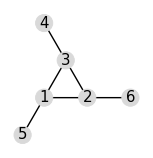
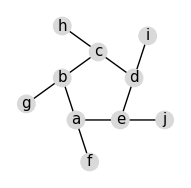
Consider the following “magic” 3-gon ring, filled with the numbers 1 to 6, and each line adding to nine.

					-Graphics-		
Working clockwise, and starting from the group of three with the numerically lowest external node (4,3,2 in this example), each solution can be described uniquely. For example, the above solution can be described by the set: 4,3,2; 6,2,1; 5,1,3.
It is possible to complete the ring with four different totals: 9, 10, 11, and 12. There are eight solutions in total.
		Total | Solution Set
9 | 4,2,3;5,3,1;6,1,2
9 | 4,3,2;6,2,1;5,1,3
10 | 2,3,5;4,5,1;6,1,3
10 | 2,5,3;6,3,1;4,1,5
11 | 1,4,6;3,6,2;5,2,4
11 | 1,6,4;5,4,2;3,2,6
12 | 1,5,6;2,6,4;3,4,5
12 | 1,6,5;3,5,4;2,4,6
By concatenating each group it is possible to form 9-digit strings; the maximum string for a 3-gon ring is 432621513.
Using the numbers 1 to 10, and depending on arrangements, it is possible to form 16- and 17-digit strings. What is the maximum 16-digit string for a “magic” 5-gon ring?

				-Graphics-

```mathematica
Block[{a,b,c,d,e,f,g,h,i,j},
  a = {0, 0};
  b = {-Cos[72°], Sin[72°]};
  c = {1/2, Sin[72°]+Sin[36°]};
  d = {1+Cos[72°], Sin[72°]};
  e = {1, 0};
  f = {Cos[72°], -Sin[72°]};
  g = {-Cos[72°]-Cos[36°], Sin[72°]-Sin[36°]};
  h = {1+Cos[72°]-2Cos[36°], Sin[72°]+2Sin[36°]};
  i = {1+2Cos[72°], 2Sin[72°]};
  j = {2, 0};
  Graphics[{
    Line[{a,b,c,d,e,a}],
    Line[{a,f}], Line[{b,g}], Line[{c,h}], Line[{d,i}], Line[{e,j}],
    EdgeForm[Thickness[0.004]],LightGray,
    Map[Disk[#,0.2]&, {a,b,c,d,e,f,g,h,i,j}],
    Black,
    Map[Inset[Style[#,15],Symbol[#]]&, CharacterRange["a","j"]]
  },ImageSize->{240, Automatic}]
]
```

```mathematica
Module[{solve,solution,decode,constraint,a,b,c,d,e,f,g,h,i,j},
    solve[total_]:=
        Solve[{
            h+c+d==total,
            i+d+e==total,
            j+e+a==total,
            f+a+b==total,
            g+b+c==total,
            1≤{a,b,c,d,e,f,g,h,i,j}≤10
        },{a,b,c,d,e,f,g,h,i,j},Integers];
    
    decode[{}]=Nothing;
    decode[sol_]:=
        FromDigits[{h,c,d,i,d,e,j,e,a,f,a,b,g,b,c}/.sol/. 10->Sequence[1,0]];
    constraint[sol_]:= 
        DuplicateFreeQ[sol]&&
        sol[h]<Min[sol[i],sol[j],sol[f],sol[g]]&&
        Max[sol[a],sol[b],sol[c],sol[d],sol[e]]≠10;
    solution[total_]:= Map[decode]@Select[constraint@*Association]@solve[total];

    Max@ParallelMap[solution,Range[14,19]]
]//AbsoluteTiming
```

{1.38548,6531031914842725}

#### 69 Totient maximum

Euler’s Totient function, ϕ(n) [Sometimes called the phi function], is used to determine the number of numbers less than n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine ϕ(9)=6.
	n | Relatively Prime | ϕ(n) | n/ϕ(n)
2 | 1 | 1 | 2
3 | 1,2 | 2 | 1.5
4 | 1,3 | 2 | 2
5 | 1,2,3,4 | 4 | 1.25
6 | 1,5 | 2 | 3
7 | 1,2,3,4,5,6 | 6 | 1.1666...
8 | 1,3,5,7 | 4 | 2
9 | 1,2,4,5,7,8 | 6 | 1.5
10 | 1,3,7,9 | 4 | 2.5
It can be seen that n=6 produces a maximum n/ϕ(n) for n≤10.
Find the value of n≤1000000 for which n/ϕ(n) is a maximum.

```mathematica
MaximalBy[Range[1000000],#/EulerPhi[#]&]
```

{510510}

#### 70 Totient permutation

Euler’s Totient function, ϕ(n) [sometimes called the phi function], is used to determine the number of positive numbers less than or equal to n which are relatively prime to n. For example, as 1, 2, 4, 5, 7, and 8, are all less than nine and relatively prime to nine, ϕ(9)=6.
The number 1 is considered to be relatively prime to every positive number, so ϕ(1)=1.
Interestingly, ϕ(87109)=79180, and it can be seen that 87109 is a permutation of 79180.
Find the value of n, 1<n<10^7, for which ϕ(n) is a permutation of n and the ratio n/ϕ(n) produces a minimum.

```mathematica
First@MinimalBy[#/EulerPhi[#]&]@Flatten@ParallelTable[
    With[{n=Prime[i]Prime[j]},
        If[Sort@IntegerDigits@EulerPhi[n]==Sort@IntegerDigits[n],n,Nothing]],
    {i,169,PrimePi[Sqrt[10^7]]},{j,i+1,PrimePi[10^7/Prime[i]]}
]//AbsoluteTiming
```

{0.296125,8319823}

#### 71 Ordered fractions

Consider the fraction, n/d, where n and d are positive integers, If n<d and HCF(n,d)=1, it is called a reduced proper fraction.
If we list the set of reduced proper fractions for d≤8 in ascending order of size, we get:
		1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8
It can be seen that 2/5 is the fraction immediately to the left of 3/7.
By listing the set of reduced proper fraction for d≤1000000 in ascending order of size, find the numerator of the fraction immediately to the left of 3/7.

```mathematica
Module[{findNum},
    findNum[t_,bestN_,bestD_,currD_,minD_]:=
        If[currD<minD,
            bestN/bestD,
            With[{currN=Floor[(Numerator[t]*currD-1)/Denominator[t]]},
                If[bestN*currD<currN*bestD,
                    With[{delta=Numerator[t]*currD-Denominator[t]*currN},
                         findNum[t,currN,currD,currD-1,Floor[currD/delta+1]]],
                     findNum[t,bestN,bestD,currD-1,minD]]]];
    findNum[t_,n_]:=findNum[t,0,1,n,1];
    Numerator@findNum[3/7,1000000]
]
```

428570

#### 72 Counting fractions

Consider the fraction, n/d, where n and d are positive integers, if n<d and HCF(n,d)=1, it is called reduced proper fraction.
It we list the set of reduced proper fractions for d≤8 in ascending order of size, we get:
		1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8
It can be seen that there are 21 elements in the set.
How many elements would be contained in the set of reduced proper fractions for d≤ 1000000?

```mathematica
ParallelSum[EulerPhi[n],{n,2,10^6}]//AbsoluteTiming
```

{0.821675,303963552391}

#### 73 Counting fractions in a range

Consider the fraction, n/d, where n and d are positive integers. If n<d and HCF(n,d)=1, it is called a reduced proper fraction.
If we list the set of reduced proper fractions for d≤8 in ascending order of size, we get:
		1/8, 1/7, 1/6, 1/5, 1/4, 2/7, 1/3, 3/8, 2/5, 3/7, 1/2, 4/7, 3/5, 5/8, 2/3, 5/7, 3/4, 4/5, 5/6, 6/7, 7/8
It can be seen that there are 3 fractions between 1/3 and 1/2.
How many fractions lie between 1/3 and 1/2 in the sorted set of reduced proper fraction for d≤12000?

```mathematica
Module[{min,max},
    min[t_,denom_]:=Ceiling[(Numerator[t]*denom+1)/Denominator[t]];
    max[t_,denom_]:=Floor[(Numerator[t]*denom-1)/Denominator[t]];
    ParallelSum[Boole[Denominator[n/d]==d],{d,5,12000},{n,min[1/3,d],max[1/2,d]}]
]//AbsoluteTiming
```

{3.49285,7295372}

#### 74 Digit factorial chains

The number 145 is well known for the property that the sum of the factorial of its digits is equal to 145:
		1!+4!+5! =1+24+120=145
Perhaps less well known is 169, in that it produces the longest chain of numbers that link back to 169; it turns out that there are only three such loops that exist:
		169→363601→1454→169
871→45361→871
872→45362→871
It is not difficult to prove that EVERY starting number will eventually get stuck in a loop. For example,
		69→363600→1454→169→363601(→1454)
78→45360→871→45361(→871)
540→145(→145)
Starting with 69 produces a chain of five non-repeating terms, but the longest non-repeating chain with a starting number below one million is sixty terms.
How many chains, with a starting number below one million, contains exactly sixty non-repeating terms?

```mathematica
Module[{chain},
    chain[1|2|145|40585]=1;
    chain[871|872|45361|45362]=2;
    chain[169|36301|1454]=3;
    chain[n_]:=chain[n]=1+chain[Total@Factorial@IntegerDigits[n]];
    ParallelSum[Boole[chain[n]==60],{n,1000000}]
]//AbsoluteTiming
```

{2.25733,402}

#### 76 Counting summations

It is possible to write five as a sum in exactly six different ways:
	4+1
3+2
3+1+1
2+2+1
2+1+1+1
1+1+1+1+1
How many different ways can on hundred be written as a sum of at least two positive integers?

```mathematica
PartitionsP[100]-1
```

190569291

#### 78 Coin partitions

Let p(n) represent the number of different ways in which n coins can be separated into piles. For example, five coins can be separated into piles in exactly seven different ways, so p(5)=7.
	ooooo
ooooo    o
ooo    oo
ooo    o    o
oo    oo    o
oo    oo    o
oo    o     o    o
o    o    o    o    o
Find the least value of n for which p(n) is divisible by one million.

```mathematica
Module[{p, penta},
    p[0|1]=1;
    
    penta[n_,k_,a_,b_,s_,sum_]/;n≥a:=
        penta[n,k+3,a+k+1,b+k,-s,sum+s*(p[n-a]+p[n-b])];
    penta[n_,k_,a_,b_,s_,sum_]:=
       If[n≥b,sum+s*p[n-b],sum];
    penta[n_]:=Mod[penta[n,4,2,1,1,0],1000000];
    
    NestWhile[#+1&,2,(p[#]=penta[#])≠0&]
] // AbsoluteTiming
```

{34.825,55374}

Note : The Mathematica program is very slow, so a equivalent Java program is listed below :

public class CoinPartitions {
	private int p[] = new int[1000000];

	private int partition(int n) {
		int k = 4;
		int a = 2;
		int b = 1;
		int s = 1;
		int sum = 0;
		
		while (n >= a) {
	   		sum += s * (p[n - a] + p[n - b]);
			a += k + 1;
			b += k;
			k += 3;
			s = -s;
		}
		if (n >= b) {
			sum += s * p[n - b];
		}
		return p[n] = sum % 1000000;
    }

	public int findParition() {
		p[0] = p[1] = 1;
		for (int n = 2; ; n++) {
			if (partition(n) == 0) {
				return n;
			}
		}
	}
	
	public static void main(String[] args) {
		CoinPartition solver = new CoinPartiton();
		System.out.println(solver.findPartition());
	}
}

#### 79 Passcode derivation

A common security method used for online banking is to ask the user for three random characters from as passcode. For example, If the passcode was 531278, they may ask for the 2nd, 3rd, and 5th characters; the expected reply would be: 317.
The text file, keylog.txt, contains fifty successful login attempts.
Given that the three characters are always asked for in order, analyse the file so as to determine the shortest possible secret passcode of unknown length.

```mathematica
keylog=ReadList["https://projecteuler.net/project/resources/p079_keylog.txt"];
FromDigits[
    {0,1,2,3,6,7,8,9}//.
    (Union[IntegerDigits[keylog]/.{a_,b_,c_}:>Sequence[{a,b},{a,c},{b,c}]]
    /.{b_,a_}:>({A___,a,B___,b,C___}:>{A,b,B,a,C}))
]
```

73162890

#### 80 Square root digital expansion

It is well known that if the square root of natural number is not an integer, then it is irrational. The decimal expansion of such square roots is infinite without any repeating pattern at all.
The square root of two is 1.41421356237309504880..., and the digital sum of the first one hundred decimal digits is 475.
For the first one hundred natural numbers, find the total of the digital sums of the first one hundred decimal digits for all the irrational square roots.

```mathematica
Module[{countDigits},
    countDigits[x_]:=0/;IntegerQ[Sqrt[x]];
    countDigits[x_]:=
        Total@IntegerDigits@Floor[Sqrt[x]*10^99];
        (* 99 is ok because all square roots under 100 only have 1 integer digit *)
    Sum[countDigits[x],{x,100}]
]
```

40886

#### 81 Path sum: two ways

In the 5 by 5 matrix below, the minimal path sum from the top left to the bottom right, by only moving to right and down, is indicated in bold red and is equal to 2427.
			(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 954 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)
Find the minimal path sum, in matrix.txt, a 31K text file containing a 80 by 80 matrix, from the top left to the bottom right by only moving right and down.

```mathematica
Module[{matrix, dim, route},
    matrix=Import["https://projecteuler.net/project/resources/p081_matrix.txt","CSV"];
    dim=Dimensions[matrix];
    
    route[row_,col_]:=route[row,col]=
        If[{row,col}==dim,
            m⟦row,col⟧,
            With[{
                down=If[row<dim⟦1⟧,route[row+1,col],Infinity],
                right=If[col<dim⟦2⟧,route[row,col+1],Infinity]
            }, m⟦row,col⟧+Min[down,right]]];
    route[1,1]
]
```

427337

#### 82 Path sum: three ways

The minimal path sum in the 5 by 5 matrix below, by starting in any cell in the left column and finishing in any cell in the right column, and only moving up, down, and right, is indicated in red and bold; the sum is equal to 994.
			(131 | 673 | 234 | 103 | 18
201 | 96 | 342 | 954 | 150
630 | 803 | 746 | 422 | 111
537 | 699 | 497 | 121 | 956
805 | 732 | 524 | 37 | 331)
Find the minimal path sum, in matrix.txt, a 31K text file containing a 80 by 80 matrix, from the left column to the right column.

```mathematica
Module[{matrix, rows, cols, index, unindex,up,down,right,encode,g},
    matrix = Import["https://projecteuler.net/project/resources/p082_matrix.txt", "CSV"];
    {rows, cols}=Dimensions[matrix];
    index[row_,col_]:=(row-1)*rows+col;
    unindex[i_]:=(i-1)~QuotientRemainder~cols+{1,1};

    up[_,{1,_}|{_,cols}]:=Nothing;
    up[weight_,{row_,col_}]:=
        {index[row,col],index[row-1,col]}->weight;
        
    down[_,{rows,_}|{_,cols}]:=Nothing;
    down[weight_,{row_,col_}]:=
        {index[row,col],index[row+1,col]}->weight;
        
    right[_,{_,cols}]:=Nothing;
    right[weight_,{row_,col_}]/;col==cols-1:=
        {index[row,col],index[row,col+1]}->weight+matrix⟦row,col+1⟧;
    right[weight_,{row_,col_}]:=
        {index[row,col],index[row,col+1]}->weight;
        
    encode[x__]:={up[x],down[x],right[x]};

    g=WeightedAdjacencyGraph@SparseArray[
            Flatten@MapIndexed[encode,matrix,{2}],
            {rows*cols,rows*cols},Infinity];

    Min@ParallelMap[GraphDistance[g,index[#⟦1⟧,1],index[#⟦2⟧,cols]]&,Tuples[Range[rows],{2}]]
]//AbsoluteTiming
```

{6.10843,260324.}

#### 85 Counting rectangles

By counting carefully it can be seen that a rectangular grid measuring 3 by 2 contains eighteen rectangles:
				-Graphics-
Although there exists no rectangular grid that contains exactly two million rectangles, find the area of the grid with the nearest solution.

```mathematica
First@First@MinimalBy[Last]@
    Map[With[{n=NSolve[#(#+1)n(n+1)/4==2*^6&&n>0,{n}]⟦1,1,2⟧},
        {#*IntegerPart[n],n-IntegerPart[n]}]&,
        Range[50,100]]
```

2772

#### 86 Cuboid route

A spider, S, sits in one corner of a cuboid room, measuring 6 by 5 by 3, and a fly, F, sits in the opposite corner. By travelling on the surfaces of the room the shortest “straight line” distance from S to F is 10 and the path is shown on the diagram.
				-Graphics-
However, there are up to three “shortest” path candidates for any given cuboid and the shortest route doesn’t always have integer length.
It can be shown that there are exactly 2060 distinct cuboids, ignoring rotations, with integer dimensions, up to a maximum size of M by M by M, for which the shortest route has integer length when M = 100. This is the least value of M for which the number of solutions first exceeds two thousand; the number of solutions when M = 99 is 1975.
Find the least value of M such that the number of solutions first exceeds one million.

```mathematica
Module[{pythagorean,pyth,triplet,count,path,total},
    (* Generate the table for all Pythagorean triplet *)
    pyth[_]={};
    pythagorean[max_]:=
        Do[If[GCD[m,n]==1,
            With[{a=m^2-n^2,b=2m n},
                If[a>max&&b>max,Break[]];
                pyth[a]=Append[pyth[a],b];
                pyth[b]=Append[pyth[b],a]]],
            {m,Infinity},{n,If[EvenQ[m],1,2],m-1,2}];

    (* Find all Pythagorean triplet for the given number *)
    triplet[n_]:=
        Select[0<#<2n&]@Flatten@Map[(n/#)pyth[#]&]@Divisors[n];
        
    (* Count the paths that confirm to the formula a^2+(b+c)^2 for a ≥ b ≥ c> 0 *)
    count[n_][m_]:=If[m>n,Floor[n-m/2]+1,Floor[m/2]];

    (* Count the Pythagorean triplet for the given number *)
    path[n_]:=Total@Map[count[n]]@triplet[n];
        
    (* Count all until total exceeds M *)
    pythagorean[10000];
    total[n_,M_]:=If[M≤0,n-1,total[n+1,M-path[n]]];
    total[1,10^6]
]
```

1818

#### 87 Prime power triples

The smallest number expressible as the sum of a prime square, prime cube, and prime fourth power is 28. In fact, there are exactly four numbers below fifty that can be expressed in such a way:
		28=2^2+2^3+2^4
33=3^2+2^3+2^4
49=5^2+2^3+2^4
47=2^2+3^3+2^4
How many numbers below fifty million can be expressed as the sum of a prime square, prime cube, and prime fourth power?

```mathematica
Module[{limit,numbers,count},
    limit=5*^7;
    numbers[_]=False;
    count=0;
    Do[
        Do[
            Do[With[{x=Prime[a]^2+Prime[b]^3+Prime[c]^4},
                If[x≥limit,Break[],
                    If[!numbers[x],
                        numbers[x]=True;count++]]],
                {c,1,PrimePi@Surd[limit,4]}],
            {b,1,PrimePi@CubeRoot[limit]}],
        {a,1,PrimePi@Sqrt[limit]}];
    count
]//AbsoluteTiming
```

{12.3034,1097343}

#### 88 Product-sum numbers

A natural number, N, that can be written as the sum and product of a given set of at least two natural numbers, {a_(1,)a_2,...,a_k} is called a product-sum number: N=a_1+a_2+...+a_k=a_1×a_2×...×a_k.
For example, 6=1+2+3=1×2×3.
For a given set of size, k, we shall call the smallest N with this property a minimal product-sum number. The minimal product-sum numbers for sets of size, k = 2, 3, 4, 5, and 6 are as follows.
		k=2:4=2×2=2+2
k=3:6=1×2×3=1+2+3
k=4:8=1×1×2×4=1+1+2+4
k=5:8=1×1×2×2×2=1+1+2+2+2
k=6:12=1×1×1×1×2×6=1+1+1+1+2+6
Hence for 2≤k≤6, the sum of all the minimal product-sum numbers is 4+6+8+12 = 30; note that 8 is only counted once in the sum.
In fact, as the complete set of minimal product-sum numbers for 2≤k≤12 is {4, 6, 8, 12, 15, 16}, the sum is 61.
What is the sum of all the minimal product-sum numbers for 2≤k≤12000?

```mathematica
Module[{partitions,summations,combine,prodsums,count,limit=12000},
    partitions[x_?PrimeQ]:={{x}};
    partitions[x_]:=partitions[x]=
        With[{f=Divisors[x]⟦2⟧},
            partitions[f,x/f]];

  partitions[f_,x_?PrimeQ]:={{f,x}};
  partitions[f_,x_]:=
        DeleteDuplicates@Map[Sort]@Catenate@Map[combine[f]]@partitions[x];
    
    combine[f_][partition_]:=
        Join[
            MapIndexed[ReplacePart[partition,#2->f#1]&,partition],
            {Prepend[partition,f],{f,Times@@partition}}];
    
    summations[n_]:=
        Map[With[{len=Length[#],sum=Total[#]},
            If[sum≤n,len+n-sum,Nothing]]&,
        partitions[n]];
        
    prodsums[_]=0;
    count=limit;
    Do[
        Scan[
            If[#≤limit&&prodsums[#]==0,
                prodsums[#]=n;
                If[--count==0,Break[]]]&,
            summations[n]],
        {n,2,Infinity}];
        
    Total@DeleteDuplicates@Table[prodsums[k],{k,2,limit}]
]//AbsoluteTiming
```

{3.13876,7587457}

#### 89 Roman numerals

For a number written in Roman numerals to be considered valid there are basic rules which must be followed. Even though the rules allow some numbers to be expressed in more than one way there is always a “best” way of writing a particular number.
For example, it would appear that there are at least six ways of writing the number sixteen:

IIIIIIIIIIIIIIII
		VIIIIIIIIIII
		VVIIIIII
		XIIIIII
		VVVI
		XVI

However, according to the rules only XIIIIII and XVI are valid, and the last example is considered to be the most efficient, as it uses the least number of numerals.
The 11K text file, roman.txt, contains one thousand numbers written in valid, but not necessarily minimal, Roman numerals; see About... Roman Numerals for the definitive rules for this problem.
Find the number of characters saved by writing each of these in their minimal form.
Note: You can assume that all the Roman numerals in the file contains no more than four consecutive identical units.

```mathematica
Module[{romans,saved},
    romans=Flatten@Import["https://projecteuler.net/project/resources/p089_roman.txt","Table"];
    Off[FromRomanNumeral::nrom];
    saved[roman_]:=StringLength[roman]-StringLength[RomanNumeral@FromRomanNumeral[roman]];
    Total@Map[saved,romans]
]
```

743

#### 92 Square digit chains

A number chain is created by continuously adding the square of the digits in a number to form a new number until it has been seen before.
For example,
	44→32→13→10→1→1
85→89→145→42→20→4→16→37→58→89
Therefore any chain that arrives at 1 or 89 will become stuck in an endless loop. What is most amazing is that EVERY starting number will eventually arrive at 1 or 89.
How many starting numbers below ten million will arrive at 89?

```mathematica
Module[{d},
    d[1]=1;
    d[89]=89;
    d[n_]:=d[n]=d[Total[IntegerDigits[n]^2]];
    ParallelSum[Boole[d[n]==89],{n,10^7}]
]//AbsoluteTiming
```

{13.2142,8581146}

#### 93 Arithmetic expressions

By using each of the digits from the set, {1, 2, 3, 4}, exactly once, and making use of the four arithmetic operations (+, −, *, /) and brackets/parentheses, it is possible to form different positive integer targets.
For example,

8 = (4 * (1 + 3)) / 2
		14 = 4 * (3 + 1 / 2)
		19 = 4 * (2 + 3) − 1
		36 = 3 * 4 * (2 + 1)

Note that concatenations of the digits, like 12 + 34, are not allowed.
Using the set, {1, 2, 3, 4}, it is possible to obtain thirty-one different target numbers of which 36 is the maximum, and each of the numbers 1 to 28 can be obtained before encountering the first non-expressible number.
Find the set of four distinct digits, a < b < c < d, for which the longest set of consecutive positive integers, 1 to n, can be obtained, giving your answer as a string: abcd.

```mathematica
Module[{calc,operators,operands,optable,comb,consecutives},
    calc[{p1_,p2_,p3_},{{{a_,b_},c_},d_}]:=p1[p2[p3[a,b],c],d];
    calc[{p1_,p2_,p3_},{a_,{{b_,c_},d_}}]:=p1[a,p2[p3[b,c],d]];
    calc[{p1_,p2_,p3_},{{a_,{b_,c_}},d_}]:=p1[p2[a,p3[b,c]],d];
    calc[{p1_,p2_,p3_},{a_,{b_,{c_,d_}}}]:=p1[a,p2[b,p3[c,d]]];
    calc[{p1_,p2_,p3_},{{a_,b_},{c_,d_}}]:=p1[p2[a,b],p3[c,d]];

    operators=Tuples[{Plus,Subtract,Times,Divide},3];
    operands=Catenate@Map[Groupings[#,2]&]@Permutations[{"a","b","c","d"}];
    optable=DeleteDuplicates@Catenate@Outer[calc,operators,operands,1];

    comb[{a_,b_,c_,d_}]:=With[{r={"a"->a,"b"->b,"c"->c,"d"->d}},
        DeleteDuplicates@Map[
            With[{x=Quiet@Check[#/.r,Infinity]},
                If[IntegerQ[x]&&Positive[x],x,Nothing]]&,
            optable]];
    
    consecutives[seq_]:=Count[0]@(Sort[seq]-Range[Length[seq]]);
    MaximalBy[consecutives@*comb]@Subsets[Range[9],{4}]
]
```

{{1,2,5,8}}

#### 97 Large non-Mersenne prime

The first known prime found to exceed one million digits was discovered in 1999, and is a Mersenne prime of the form 2^6972593−1; it contains exactly 2,098,960 digits. Subsequently other Mersenne primes, of the form 2^p-1, have been found which contain more digits.
However, in 2004 there was found a massive non-Mersenne prime which contains 2,357,207 digits: 28433×2^7830457+1.
Find the last ten digits of this prime number.

```mathematica
FromDigits@Take[IntegerDigits[28433 2^7830457+1],-10]
```

8739992577

#### 98 Anagramic squares

By replacing each of the letters in the word CARE with 1, 2, 9, and 6 respectively, we form a square number: 1296 = 36^2. What is remarkable is that, by using the same digital substitutions, the anagram, RACE, also forms a square number: 9216 = 96^2. We shall call CARE (and RACE) a square anagram word pair and specify further that leading zeroes are not permitted, neither may a different letter have the same digital value as another letter.
Using words.txt, a 16K text file containing nearly two-thousand common English words, find all the square anagram word pairs (a palindromic word is NOT considered to be an anagram of itself).
What is the largest square number formed by any member of such a pair?
NOTE: All anagrams formed must be contained in the given text file.

```mathematica
Module[{words,squares,replaceable,squarePair,compareList,anagram},
    words=Map[ToCharacterCode]@Flatten@Import[
        "https://projecteuler.net/project/resources/p098_words.txt","CSV"];
    
    squares[n_]:=squares[n]=
        Table[IntegerDigits[i^2],{i,Floor@Sqrt[10^n-1],Ceiling@Sqrt[10^(n-1)],-1}];
        
    replaceable[code_,value_]:=
        With[{rule=DeleteDuplicates@Thread[code->value]},
            DuplicateFreeQ[rule⟦All,1⟧]&&DuplicateFreeQ[rule⟦All,2⟧]];
    
    squarePair[x_,y_]:=
        With[{sqs=squares[Length[x]]},
            SelectFirst[sqs,replaceable[x,#]&&MemberQ[sqs,y/.Thread[x->#]]&,Nothing]];
    
    compareList[{},{}]=0;
    compareList[{},{__}]=-1;
    compareList[{__},{}]=1;
    compareList[{a_,as___},{a_,bs___}]:=compareList[{as},{bs}];
    compareList[{a_,___},{b_,___}]:=a-b;
    
    anagram[word_]:=With[{w=Sort[word]},
        Map[If[compareList[word,#]>0&&Sort[#]==w,
                squarePair[word,#],
                Nothing]&,
            words]];
        
    Max@Map[FromDigits]@Catenate@ParallelMap[anagram,words]
]//AbsoluteTiming
```

{6.10794,18769}

#### 99 Largest exponential

Comparing two numbers written in index form like 2^11 and 3^7 is not difficult, as any calculator would confirm that 2^11=2048<3^7=2187.
However, confirming that 632382^518061>519432^525806 would be much more difficult, as both numbers contain over three million digits.
Using base_exp.txt , a 22K text file containing one thousand lines with a base/exponent pair on each line, determine which line number has the greatest numerical value.
NOTE: The first two lines in the file represent the numbers in the example given above.

```mathematica
Module[{baseexp},
    baseexp=Import["https://projecteuler.net/project/resources/p099_base_exp.txt","CSV"];
    MaximalBy[Last]@MapIndexed[#2⟦1⟧->N[#1⟦2⟧Log[#1⟦1⟧]]&,baseexp]//First//First
]
```

709

#### 100 Arranged probability

If a box contains twenty-one coloured discs, composed of fifteen blue discs and six red discs, and two discs were taken at random, it can be seen that the probability of taking two blue discs, P(BB)=(15/21)×(14/20)=1/2.
The next such arrangement, for which there is exactly 50% chance of taking two blue discs at random, is a box containing eighty-five blue discs and thirty-five red discs.
By finding the first arrangement to contain over 10^12=1000000000000 discs in total, determine the number of blue discs that the box would contain.

```mathematica
Solve[(b(b-1))/(n(n-1))==1/2&&0<b<10^12<n,{b,n},Integers]
```

{{b→756872327473,n→1070379110497}}

#### 104 Pandigital Fibonacci ends

The Fibonacci sequence is defined by the recurrence relation:
		F_n=F_(n-1)+F_(n-2), where F_1=1 and F_2=1.
It turns out that F_541, which contains 113 digits, is the first Fibonacci number for which the last nine digits are 1-9 pandigital (contain all the digits 1 to 9, but not necessarily in order). And F_2749, which contains 575 digits, is the first Fibonacci number for which the first nine digits are 1-9 pandigital.
Given that F_k is the first Fibonacci number for which the first nine digits AND the last nine digits are 1-9 pandigital, find k.

```mathematica
Module[{pandigitalQ,search},
    pandigitalQ[digits_List]:=Sort[digits]==Range[9];
    search[a_,b_,n_]:=
        If[pandigitalQ@IntegerDigits[a] && pandigitalQ@Take[IntegerDigits@Fibonacci[n],9],
            n,
            search[b,Mod[a+b,10^9],n+1]];
    Block[{$IterationLimit=Infinity},search[1,1,1]]
]//AbsoluteTiming
```

{1.99584,329468}

#### 206 Concealed Square

Find the unique positive integer whose square has the form 1 _ 2 _ 3 _ 4 _ 5 _ 6 _ 7 _ 8 _ 9 _ 0, where each “_” is a single digit.

```mathematica
Module[{lbound,ubound,pattern},
    lbound=Floor[Sqrt[1020304050607080900]/100]*100+70;
    ubound=Floor[Sqrt[1929394959697989990]/100]*100+70;
    pattern=Riffle[Append[Range[9],0],_];
    SelectFirst[MatchQ[IntegerDigits[#^2],pattern]&]@Range[ubound,lbound,-100]
]//AbsoluteTiming
```

{0.196543,1389019170}

#### 243 Resilience

A positive fraction whose numerator is less than its denominator is called a proper fraction.
For any denominator, d, there will be d−1 proper fractions; for example, with d = 12:
	1/12,2/12,3/12,4/12,5/12,6/12,7/12,8/12,9/12,10/12,11/12
We shall call a fraction that cannot be cancelled down a resilient fraction.
Furthermore we shall define the resilience of a denominator, R(d), to be the ratio of its proper fractions that are resilient; for example, R(12) = 4/11 .
In fact, d = 12 is the smallest denominator having a resilience R(d) < 4/10 .
Find the smallest denominator d, having a resilience R(d) < 15499/94744 .

```mathematica
Module[{R,findInRange,find},
    R[n_]:=EulerPhi[n]/(n-1);
    findInRange[i_,f_]:=
        With[{step=Times@@Prime@Range[i]},
            NestWhile[#+step&,step,R[#]≥f&,1,Prime[i+1]-1]];
    find[f_]:=
        Do[With[{d=findInRange[i,f]},If[R[d]<f,Return[d]]],{i,1,Infinity}];
    find[15499/94744]
]
```

892371480